# Finite Rod, Albedo Problem, Anisotropic Scattering

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
Eugene d’Eon 
www.eugenedeon.com

## Exponential Random Flight

## Notation

α - single-scattering albedo
Σt - extinction coefficient
x - position coordinate in rod (source at x = 0)
a - length of the rod
g - ‘mean cosine’ of scattering

## Analytic solutions

### Reflectance/Transmittance

```mathematica
R[a_,α_,Σt_,g_]:=((1-g) α)/(2-α-g α+2 √((1-α) (1-g α)) Coth[a √((1-α) (1-g α)) Σt])
```

```mathematica
T[a_,α_,Σt_,g_]:=2/(2 Cosh[a √((-1+α) (-1+g α)) Σt]+((-2+α+g α) Sinh[a √(-1+α) √(-1+g α) Σt])/(√((-1+α) (-1+g α))))
```

```mathematica
R[a_,α_,Σt_,g_,n_]:=α^n(SeriesCoefficient[R[a,A,Σt,g],{A,0,n}]/.A->α);
T[a_,α_,Σt_,g_,n_]:=α^n(SeriesCoefficient[T[a,A,Σt,g],{A,0,n}]/.A->α)
```

### ‘Radiance’

```mathematica
LR[x_,α_,Σt_,a_,g_]:=-((ⅇ^(-(a+x) √((-1+α) (-1+g α)) Σt) √((-1+α)/(-1+g α)) (-2 √(-1+α) √(-1+g α) Cosh[(a-x) √(-1+α) √(-1+g α) Σt]+(-2+α+g α) Sinh[(a-x) √(-1+α) √(-1+g α) Σt]) (√(-1+α) √(-1+g α) Cosh[(a+x) √(-1+α) √(-1+g α) Σt]+√((-1+α) (-1+g α)) Sinh[(a+x) √(-1+α) √(-1+g α) Σt]))/((-1+α) (2 (-1+α) √((-1+g α)/(-1+α)) Cosh[a √((-1+α) (-1+g α)) Σt]+(-2+α+g α) Sinh[a √((-1+α) (-1+g α)) Σt])))
```

```mathematica
LL[x_,α_,Σt_,a_,g_]:=(ⅇ^(-(a+x) √((-1+α) (-1+g α)) Σt) (ⅇ^(2 a √((-1+α) (-1+g α)) Σt)-ⅇ^(2 x √((-1+α) (-1+g α)) Σt)) √((-1+α)/(-1+g α)) (-√((-1+g α)/(-1+α))+g α √((-1+g α)/(-1+α))+√((-1+α) (-1+g α))))/(2 (2 (-1+α) √((-1+g α)/(-1+α)) Cosh[a √((-1+α) (-1+g α)) Σt]+(-2+α+g α) Sinh[a √((-1+α) (-1+g α)) Σt]))
```

### Fluence

```mathematica
ϕ[x_,α_,Σt_,a_,g_]:=LR[x,α,Σt,a,g]+LL[x,α,Σt,a,g]
```

## Monte Carlo comparisons

```mathematica
SetDirectory["/Users/eug/Documents/research/transport/rod/finiterod/albedoProblem"]
```

/Users/eug/Documents/research/transport/rod/finiterod/albedoProblem

```mathematica
ppoints[xs_,dx_,maxx_,Σt_]:=Table[{dx(i-1)+0.5dx,(1/Σt)xs[[i]]},{i,1,Length[xs]}][[1;;-2]]
```

```mathematica
fs=FileNames["data/finiterod_albedoproblem_anisotropicscatter_exp_c0.7_mut1_*"];
```

### Reflectance/Transmittance

```mathematica
MCR[f_]:=Module[{data,a},
data=Import[f,"Table"];
a=data[[2,5]];
{a,data[[3,4]]}
];
MCT[f_]:=Module[{data,a},
data=Import[f,"Table"];
a=data[[2,5]];
{a,data[[4,4]]}
]
```

```mathematica
Rs=Table[MCR[f],{f,fs}];
Ts=Table[MCT[f],{f,fs}];
```

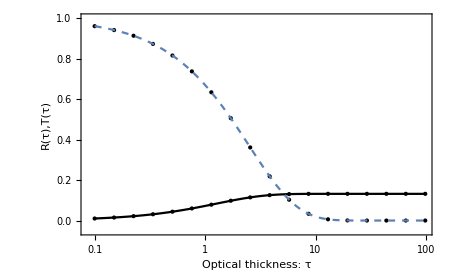

```mathematica
vizfiniterodRTaniso=Show[
ListLogLinearPlot[Rs,PlotRange->{-0.05,1},PlotStyle->{Black,PointSize[Medium]}],
ListLogLinearPlot[Ts,PlotRange->{-0.05,1},PlotStyle->{Black,PointSize[Medium]}],
LogLinearPlot[R[a,0.7,1,0.7],{a,0.1,100},PlotStyle->Black],
LogLinearPlot[T[a,0.7,1,0.7],{a,0.1,100},PlotStyle->Dashed],
ImageSize->450,
Frame->True,FrameLabel->{{"R(τ),T(τ)",},{"Optical thickness: τ","Total Reflectance/Transmittance (R/T): anisotropically-scattering finite rod (g = 0.7)"}}
]
```

```mathematica
Export["/Users/eug/Documents/research/transport/notes/img/finiterod_albedoproblem_anisoscatter_RT_varytau.pdf",vizfiniterodRTaniso,ImageSize->450]
```

/Users/eug/Documents/research/transport/notes/img/finiterod_albedoproblem_anisoscatter_RT_varytau.pdf

```mathematica
fs2=FileNames["data/finiterod_albedoproblem_anisotropicscatter_exp_*length2.6*"];
```

```mathematica
MCR2[f_]:=Module[{data,a},
data=Import[f,"Table"];
a=data[[2,3]];
{a,data[[3,4]]}
];
MCT2[f_]:=Module[{data,a},
data=Import[f,"Table"];
a=data[[2,3]];
{a,data[[4,4]]}
]
```

```mathematica
Rs2=Table[MCR2[f],{f,fs2}];
Ts2=Table[MCT2[f],{f,fs2}];
```

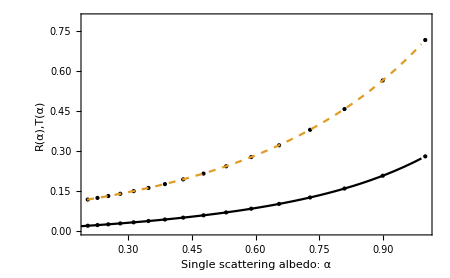

```mathematica
a=2.6;
mut=1;
finiterodvarycplot=Show[
ListPlot[Rs2,PlotRange->{0,0.8},PlotStyle->{Black,PointSize[Medium]}],
ListPlot[Ts2,PlotStyle->{Black,PointSize[Medium]}],
Plot[{R[a,c,mut,0.7],T[a,c,mut,0.7]},{c,0.01,.99},PlotRange->{0,1},PlotStyle->{Black,Dashed}],
ImageSize->450,
Frame->True,FrameLabel->{{"R(α),T(α)",},{"Single scattering albedo: α","Total Reflectance/Transmittance (R/T): anisotropically-scattering (g = 0.7) finite rod"}}
]
```

```mathematica
Export["/Users/eug/Documents/research/transport/notes/img/finiterod_albedoproblem_anisoscatter_RT_varyc.pdf",finiterodvarycplot,ImageSize->450]
```

/Users/eug/Documents/research/transport/notes/img/finiterod_albedoproblem_anisoscatter_RT_varyc.pdf

```mathematica
fs3=FileNames["data/finiterod_albedoproblem_anisotropicscatter_exp_*length1.2*"];
```

```mathematica
MCR3[f_]:=Module[{data,g},
data=Import[f,"Table"];
g=data[[1,-1]];
{g,data[[3,4]]}
];
MCT3[f_]:=Module[{data,g},
data=Import[f,"Table"];
g=data[[1,-1]];
{g,data[[4,4]]}
]
```

```mathematica
Rs3=Table[MCR3[f],{f,fs3}];
Ts3=Table[MCT3[f],{f,fs3}];
```

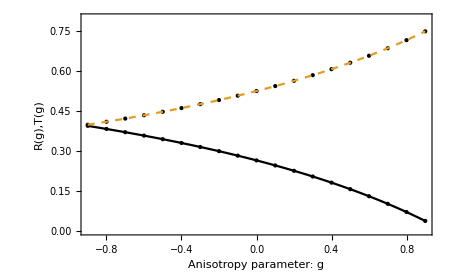

```mathematica
a=1.2;
mut=1;
c=0.8;
finiterodvarygplot=Show[
ListPlot[Rs3,PlotRange->{0,0.8},PlotStyle->{Black,PointSize[Medium]}],
ListPlot[Ts3,PlotStyle->{Black,PointSize[Medium]}],
Plot[{R[a,c,mut,g],T[a,c,mut,g]},{g,-0.9,0.9},PlotRange->{0,1},PlotStyle->{Black,Dashed}],
ImageSize->450,
Frame->True,FrameLabel->{{"R(g),T(g)",},{"Anisotropy parameter: g","Total Reflectance/Transmittance (R/T): anisotropically-scattering finite rod (c = 0.8, a = 1.2)"}}
]
```

```mathematica
Export["/Users/eug/Documents/research/transport/notes/img/finiterod_albedoproblem_anisoscatter_RT_varyg.pdf",finiterodvarygplot,ImageSize->450]
```

/Users/eug/Documents/research/transport/notes/img/finiterod_albedoproblem_anisoscatter_RT_varyg.pdf

### Select simulation

```mathematica
fs=FileNames["data/finiterod_albedoproblem_anisotropicscatter_exp_c0.7_mut0.8*"];
filename=fs[[1]];
data=Import[filename,"Table"];
Σt=data[[1,11]];
α=data[[2,3]];
a=data[[2,5]];
dx=data[[2,7]];
numcollorders=data[[2,11]];
nummoments=data[[2,13]];
g=data[[1,-1]];

densmom=data[[11]];
```

### Internal Distributions

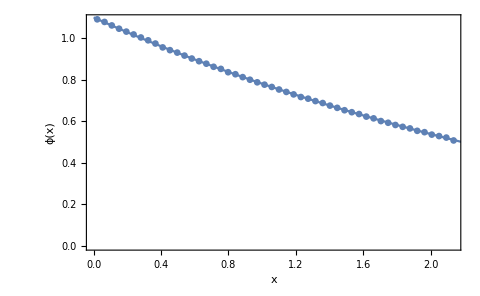

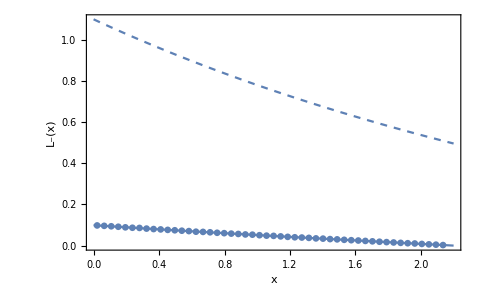

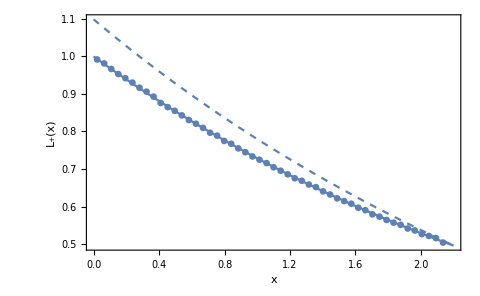

```mathematica
pointsCL = data[[10]];
(* divide by Σt to convert collision density into L *)
plotpointsCL=ppoints[pointsCL,dx,a,Σt];
pointsCR = data[[12]];
plotpointsCR=ppoints[pointsCR,dx,a,Σt];
(* divide by Σt to convert collision density into fluence *)
plotpointsϕ=ppoints[pointsCL+pointsCR,dx,maxx,Σt];

plotϕ=Show[
ListPlot[plotpointsϕ,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[ϕ[x,α,Σt,a,g],{x,0,a},PlotRange->All]
,Frame->True,
FrameLabel->{{ϕ[x],},{x,"Finite rod, albedo problem, anisotropic scattering, fluence ϕ[x]\n α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", a = "<>ToString[a]<>", g = "<>ToString[g]}}
]

plotLL=Show[
ListPlot[plotpointsCL,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[LL[x,α,Σt,a,g],{x,0,a},PlotRange->All],
Plot[ϕ[x,α,Σt,a,g],{x,0,a},PlotRange->All,PlotStyle->Dashed]
,Frame->True,
FrameLabel->{{SubMinus[L][x],},{x,"Finite rod, albedo problem, anisotropic scattering, L_-[x]\n α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", a = "<>ToString[a]<>", g = "<>ToString[g]}},PlotRange->All
]

plotLR=Show[
ListPlot[plotpointsCR,PlotRange->All,PlotStyle->PointSize[.01]],
Plot[LR[x,α,Σt,a,g],{x,0,a},PlotRange->All],
Plot[ϕ[x,α,Σt,a,g],{x,0,a},PlotRange->All,PlotStyle->Dashed]
,Frame->True,
FrameLabel->{{SubPlus[L][x],},{x,"Finite rod, albedo problem, anisotropic scattering, L_+[x]\n α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]<>", a = "<>ToString[a]<>", g = "<>ToString[g]}},PlotRange->All
]
```

```mathematica
Export["/Users/eug/Documents/research/transport/notes/img/finiterod_albedoproblem_anisoscatter_LL.pdf",plotLL,ImageSize->400]
```

/Users/eug/Documents/research/transport/notes/img/finiterod_albedoproblem_anisoscatter_LL.pdf

```mathematica
Export["/Users/eug/Documents/research/transport/notes/img/finiterod_albedoproblem_anisoscatter_LR.pdf",plotLR,ImageSize->400]
```

/Users/eug/Documents/research/transport/notes/img/finiterod_albedoproblem_anisoscatter_LR.pdf

```mathematica
Export["/Users/eug/Documents/research/transport/notes/img/finiterod_albedoproblem_anisoscatter_phi.pdf",plotϕ,ImageSize->400]
```

/Users/eug/Documents/research/transport/notes/img/finiterod_albedoproblem_anisoscatter_phi.pdf

### Nth-scattered Reflectance

```mathematica
Rs=N[{data[[6]]}];
ns=Table[n,{n,0,numcollorders-1}];
analytic=Table[R[a,α,Σt,g,n],{n,ns}];
j=Join[{ns},{analytic},Rs];
TableForm[
Join[{{"n","analytic","MC"}},Transpose[j]]
]
```

n | analytic | MC
0 | 0. | 0.
1 | 0.050946 | 0.0510135
2 | 0.0270583 | 0.0270461
3 | 0.0128058 | 0.0128372
4 | 0.00533047 | 0.0053576
5 | 0.00196362 | 0.0019582
6 | 0.000651268 | 0.0006525
7 | 0.000199191 | 0.0001993
8 | 0.0000577824 | 0.0000588
9 | 0.0000163603 | 0.0000142

### Nth-scattered Transmittance

```mathematica
Ts=N[{data[[8]]}];
ns=Table[n,{n,0,numcollorders-1}];
analytic=Table[Re[T[a,α,Σt,g,n]],{n,ns}];
j=Join[{ns},{analytic},Ts];
TableForm[
Join[{{"n","analytic","MC"}},Transpose[j]]
]
```

n | analytic | MC
0 | 0.172045 | 0.172166
1 | 0.180165 | 0.180095
2 | 0.0955436 | 0.0954108
3 | 0.0346701 | 0.0346257
4 | 0.00995504 | 0.0099563
5 | 0.0025379 | 0.0025378
6 | 0.000641365 | 0.0006422
7 | 0.000173425 | 0.0001761
8 | 0.0000504535 | 0.0000521
9 | 0.0000151766 | 0.0000143

### Nth order fluence/density

```mathematica
nthϕ=data[[16+numcollorders+1;;16+2numcollorders]];
```

0.00073969 ⅇ^(-0.8 x) (42.2305-5.65 ⅇ^(1.6 x)+33.7844 x+1. ⅇ^(1.6 x) x-0.107029 Cosh[1.76-0.8 x] Cosh[1.76+0.8 x]+0.176471 x Cosh[1.76-0.8 x] Cosh[1.76+0.8 x]+4.53333 x^2 Cosh[1.76-0.8 x] Cosh[1.76+0.8 x]+0.113559 Cosh[1.76+0.8 x] Sinh[1.76-0.8 x]+0.176471 x Cosh[1.76+0.8 x] Sinh[1.76-0.8 x]+4.53333 x^2 Cosh[1.76+0.8 x] Sinh[1.76-0.8 x]-0.107029 Cosh[1.76-0.8 x] Sinh[1.76+0.8 x]+0.176471 x Cosh[1.76-0.8 x] Sinh[1.76+0.8 x]+4.53333 x^2 Cosh[1.76-0.8 x] Sinh[1.76+0.8 x]+0.113559 Sinh[1.76-0.8 x] Sinh[1.76+0.8 x]+0.176471 x Sinh[1.76-0.8 x] Sinh[1.76+0.8 x]+4.53333 x^2 Sinh[1.76-0.8 x] Sinh[1.76+0.8 x])

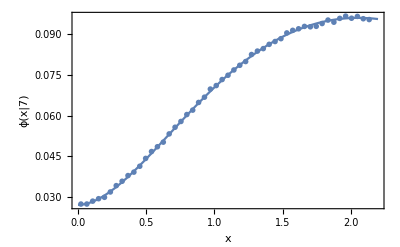

```mathematica
(* choose order:*)
n=2;

Clear[c];
phin=SeriesCoefficient[ϕ[x,c,Σt,a,g],{c,0,n}] α^n
plotphin=Show[
ListPlot[ppoints[nthϕ[[n+2]],dx,a,Σt],PlotRange->All,PlotStyle->PointSize[.01]],
Plot[phin,{x,0,a},PlotRange->All]
,Frame->True,
FrameLabel->{{ϕ["x|7"],},{x,"Semi-Infinite Rod, isotropic point, isotropic scattering, ϕ[x|"<>ToString[n]<>"], α = "<>ToString[α]<>", Σ_t = "<>ToString[Σt]}},PlotRange->All
]
```